# Simulation of droplet by GPELAB

Authors: Zhichao Guo <guozc12@gmail.com>
Version: 1.0
Date: 2019.12.11 - 2019.12.23

This Mathematica notebook is used for constructing GPELAB simulation for droplet. 
By modifying original double BEC of Rb and Na simulation from Xiaoke Li, we add LHY(Lee-Huang-Yang) tern into the calculation for simulating droplet sample.

## Constants and Global Functions

### Global Function

```mathematica
ClearAll["Global`*"];
```

```mathematica
Cons={
h->6.626070040*10^-34,
ℏ->h/(2π),
c->299792458,
α->e^2/(4π Subscript[ϵ, 0] ℏ c),
mp->1.672621898*10^-27,
amu->1.660539040*10^-27,
me->9.10938356*10^-31,
a0->(4π Subscript[ϵ, 0] ℏ^2)/(me e^2),
E0->(e^4 me)/(32 π^2 ℏ^2 Subscript[ϵ, 0]^2),
e->1.6021766208*10^-19,
Subscript[ϵ, 0]->1/(Subscript[μ, 0] c^2),
Subscript[μ, 0]->4π*10^-7,
μN->5.050783699*10^-27,
Subscript[μ, B]->9.274009994*10^-24,
Subscript[g, e]->2,
Z->1
};
```

### Rb Na Feshbach resonance

Here are Rb and Na mass

```mathematica
mRb=86.909187;(*amu*)(*Rb mass in atomic mass unit*)
mNa=22.989767;(*amu*)(*Na mass in atomic mass unit*)
```

Here are basic parameter for Rb Na scattering:

```mathematica
B0=347.635; (*G*)(*Rb Na Feshbach resonance(FR) point*)
B01 =478.827;(*G*)(*Rb Na Feshbach resonance peak2*)
Δ=-5.20217;(*G*)(*Rb Na FR width*)
Δ01=-4.80701;(*G*)(*Rb Na FR width 2*)
Subscript[a, RR]=100.4;(*100.4;*)(*a0*)(*Rb Rb Background scattering length*)
Subscript[a, NN]=54.5;(*54.5;*)(*a0*)(*Na Na Background scattering length*)
Subscript[a, RN]=66.77; (*a0 66.77*)(*Rb Na Background scattering length*)
```

We calculate and plot following parameters varying with B-field:

a_(Rb-Na)(B)=a_RN(1+Δ/(B-B0))(1+Δ01/(B-B01))

g_(Rb-Na)=(2π ℏ^2 a_RN(1+Δ/(B-B0))(1+Δ01/(B-B01)))/(m_Rb m_Na/(m_Rb+m_Na))

δg=g_(Rb-Na)+√(g_Rb g_Na)

We find that for δg=0, B-field is at

```mathematica
Bδg=Last@NSolve[(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01)))/(mNa*mRb/(mNa+mRb))+√(Subscript[a, NN]/(mNa/2)*Subscript[a, RR]/(mRb/2))==0,B]
```

{B→350.419}

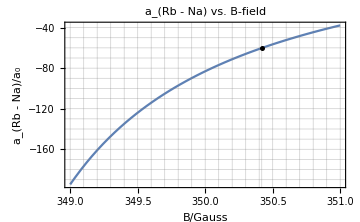

```mathematica
Plot[(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01))),{B,349,351},Frame->True,GridLines->{Evaluate@Table[x,{x,349,351,0.1}]~Join~{{B/.Bδg,Thick}},Table[x,{x,-200,-30,10}]},PlotLabel->Style["a_(Rb - Na) vs. B-field",FontSize->30],Epilog->{PointSize[0.01],Point[{B,(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01)))}/.Bδg]},FrameLabel->{Style["B/Gauss",FontFamily->"Goudy Old Style",FontSize->30],Style["a_(Rb - Na)/a_0",FontFamily->"Goudy Old Style",FontSize->30]},ImageSize->Medium]
```

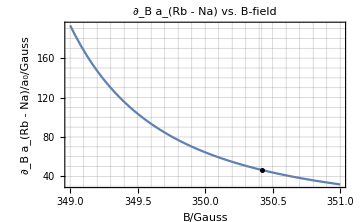

```mathematica
Plot[Evaluate@(D[(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01))), B]),{B,349,351},Frame->True,GridLines->{Evaluate@Table[x,{x,349,351,0.1}]~Join~{{B/.Bδg,Thick}},Table[x,{x,30,230,10}]},PlotLabel->"∂_B a_(Rb - Na) vs. B-field",Epilog->{PointSize[0.01],Point[{B,Evaluate@(D[(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01))), B])}/.Bδg]},FrameLabel->{Style["B/Gauss",FontFamily->"Goudy Old Style",FontSize->16],Style["∂_B a_(Rb - Na)/a_0/Gauss",FontFamily->"Goudy Old Style",FontSize->16]},ImageSize->Medium]
```

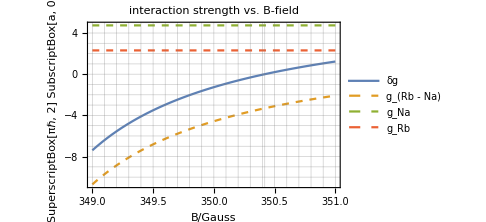

```mathematica
Plot[{(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01)))/(mNa*mRb/(mNa+mRb))+√(Subscript[a, NN]/(mNa/2)*Subscript[a, RR]/(mRb/2)),(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01)))/(mNa*mRb/(mNa+mRb)),Subscript[a, NN]/(mNa/2),Subscript[a, RR]/(mRb/2)},{B,349,351},Frame->True,ImageSize->Medium,PlotLabel->"interaction strength vs. B-field",GridLines->{Evaluate@Table[x,{x,349,351,0.1}]~Join~{{B/.Bδg,Thick}},Table[x,{x,-12,5,1}]},PlotStyle->{,Dashed,Dashed,Dashed},PlotLegends->Placed[{"δg","g_(Rb - Na)","g_Na","g_Rb"},Below],FrameLabel->{Style["B/Gauss",FontFamily->"Goudy Old Style",FontSize->16],Style["g/(2 SuperscriptBox[πℏ, 2] SubscriptBox[a, 0])/amu",FontFamily->"Goudy Old Style",FontSize->16]}]
```

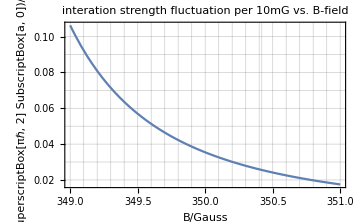

```mathematica
Plot[Evaluate@D[(0.01(Subscript[a, RN](1+Δ/(B-B0))(1+Δ01/(B-B01)))/(mNa*mRb/(mNa+mRb))), B],{B,349,351},Frame->True,ImageSize->Medium,PlotLabel->"interation strength fluctuation per 10mG vs. B-field",GridLines->{Evaluate@Table[x,{x,349,351,0.1}]~Join~{{B/.Bδg,Thick}},Table[x,{x,0.02,0.12,0.01}]},FrameLabel->{Style["B/Gauss",FontFamily->"Goudy Old Style",FontSize->16],Style["∂_B δg/(2 SuperscriptBox[πℏ, 2] SubscriptBox[a, 0])/(amu*10  mG)",FontFamily->"Goudy Old Style",FontSize->16]}]
```

## LHY term of Rb-Na Bose Mixture

### Hamiltonian

Hamiltonian for BEC with two components is

H_tot=∑_k ϵ_(1,k)(â)_(1,k)†(â)_(1,k)+g_11/(2V)∑_{k_i} (â)_(1,k_1)^+(â)_(1,k_2)^+(â)_(1,k_3)(â)_(1,k_4)+∑_k ϵ_(2,k)(â)_(2,k)†(â)_(2,k)+g_22/(2V)∑_{k_i} (â)_(2,k_1)^+(â)_(2,k_2)^+(â)_(2,k_3)(â)_(2,k_4)+g_12/V∑_{k_i} (â)_(2,k_1)^+(â)_(1,k_2)^+(â)_(1,k_3)(â)_(2,k_4)

where k_1+k_2=k_3+k_4, satisfy momentum conservation. g_ii represent intra-interaction strength, and g_12 for inter-interaction. (â)_(i,k)^+((â)_(i,k)) denote the ladder operator for i^th component.

(â)_(i,0)=√N_i

After extended Bogoliubov transformation, we have

H=(g_11 N_1^2+g_22 N_2^2+2 g_12 N_1 N_2)/(2V)+1/2∑_(k≠0) (E_++E_--(ℏ^2 k^2)/(2 m_1)-(ℏ^2 k^2)/(2 m_2)-(g_11 N_1+g_22 N_2)/V)+∑_(k≠0) E_(+,k)(â)_(+,k)†(â)_(+,k)+∑_(k≠0) E_(-,k)(â)_(-,k)†(â)_(-,k)

where first term gives mean-field ground state energy; second term gives LHY correction; last two terms provide two branches of excitation spectrum. Details of parameters in above formula are listed here:

E_±=√((ω_1^2+ω_2^2)/2±√(((ω_1^2-ω_2^2)/2)^2+(g_12^2 N_1 N_2)/V^2(ℏ^2 k^4)/(m_1 m_2)))
ω_i=√((ℏ^2 k^2)/(2 m_i)((ℏ^2 k^2)/(2 m_i)+(2 g_ii N_i)/V))

### Ground state energy

Ground state energy is

E_GS=(g_11 N_1^2+g_22 N_2^2+2 g_12 N_1 N_2)/(2V)+1/2∑_(k≠0) (E_++E_--(ℏ^2 k^2)/(2 m_1)-(ℏ^2 k^2)/(2 m_2)-(g_11 N_1+g_22 N_2)/V)

After renormalization we have the second term, LHY term, which can be rewritten with (EquationNumbered) in

E_LHY=1/2∑_(k≠0) (√((ω_1^2+ω_2^2)/2+√(((ω_1^2-ω_2^2)/2)^2+g_12^2 n_1 n_2(ℏ^4 k^4)/(m_1 m_2)))+√((ω_1^2+ω_2^2)/2-√(((ω_1^2-ω_2^2)/2)^2+g_12^2 n_1 n_2(ℏ^4 k^4)/(m_1 m_2)))-(ℏ^2 k^2)/(2 m_1)-(ℏ^2 k^2)/(2 m_2)-g_11 n_1-g_22 n_2+(m_1 g_11^2 n_1^2+m_2 g_22^2 n_2^2+4(m_1 m_2)/(m_1+ m_2)g_12^2 n_1 n_2)/(ℏ^2 k^2))

Replace summation by integral (∑_k →V∫ⅆ k⃗), we have

ℰ_LHY=E_LHY/V=∫_0^(k_c→ ∞) k^2/(4 π^2)(√((ω_1^2+ω_2^2)/2+√(((ω_1^2-ω_2^2)/2)^2+g_12^2 n_1 n_2(ℏ^4 k^4)/(m_1 m_2)))+√((ω_1^2+ω_2^2)/2-√(((ω_1^2-ω_2^2)/2)^2+g_12^2 n_1 n_2(ℏ^4 k^4)/(m_1 m_2)))-(ℏ^2 k^2)/(2 m_1)-(ℏ^2 k^2)/(2 m_2)-g_11 n_1-g_22 n_2+(m_1 g_11^2 n_1^2+m_2 g_22^2 n_2^2+4(m_1 m_2)/(m_1+ m_2)g_12^2 n_1 n_2)/(ℏ^2 k^2))ⅆk

For simplicity, we reform it into dimensionless form

ℰ_LHY=C_1∫_0^k_c 15/32(k̃)^2(√(1/2( (k̃)^2/2((k̃)^2/2+2)+1/γ^2(k̃)^2/2((k̃)^2/2+2y γ))+√((1/2( (k̃)^2/2((k̃)^2/2+2)-1/γ^2(k̃)^2/2((k̃)^2/2+2y γ)))^2+(x y)/γ(k̃)^4))+√(1/2( (k̃)^2/2((k̃)^2/2+2)+1/γ^2(k̃)^2/2((k̃)^2/2+2y γ))-√((1/2( (k̃)^2/2((k̃)^2/2+2)-1/γ^2(k̃)^2/2((k̃)^2/2+2y γ)))^2+(x y)/γ(k̃)^4))-(k̃)^2/2(1+1/γ)-1-y+(1+γ y^2+(4x y γ)/(1+γ))/(k̃)^2)ⅆ k̃

where

C_1=8/(15 π^2)g_11(n_1((√(m_1 g_11 n_1))/ℏ))^3, γ=m_2/m_1, x=g_12^2/(g_11 g_22), y=(g_22 n_2)/(g_11 n_1), k̃=(ℏ k)/(√(m_1 g_11 n_1))

using f(m_2/m_1,g_12^2/(g_11 g_22),(g_22 n_2)/(g_11 n_1)) replacing the tedious integral, we have

ℰ_LHY=8/(15 π^2)((m_1^(3/2)(g_11 n_1))^(5/2))/ℏ^3 f(γ,x,y)

### Calculation(calculated by MMA, not full spectrum)

In this section, we will calculate f(γ,x,y) numerically for our Rb-Na Bose mixture system

First we do this integration and check its convergence. We plot f(γ,x,y) with increasing upper bound of integration k_C to test its convergence.

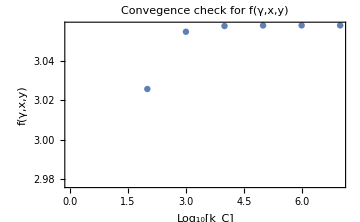

```mathematica
ListPlot[Table[NIntegrate[(15/32 k^2 (-1-y-1/2 k^2 (1+1/γ)+(1+y^2 γ+(4 x y γ)/(1+γ))/k^2+√(1/2 (1/2 k^2 (2+k^2/2)+(k^2 (k^2/2+2 y γ))/(2 γ^2))-√((k^4 x y)/γ+1/4 (1/2 k^2 (2+k^2/2)-(k^2 (k^2/2+2 y γ))/(2 γ^2))^2))+√(1/2 (1/2 k^2 (2+k^2/2)+(k^2 (k^2/2+2 y γ))/(2 γ^2))+√((k^4 x y)/γ+1/4 (1/2 k^2 (2+k^2/2)-(k^2 (k^2/2+2 y γ))/(2 γ^2))^2))))/.{γ->2645263152674527/10000000000000000,y->1432507661901817/1000000000000000,x->1},{k,√2 √(-1-y γ+√(1-2 y γ+4 x y γ+y^2 γ^2))/.{γ->2645263152674527/10000000000000000,y->1432507661901817/1000000000000000,x->1},10^kc},PrecisionGoal->100,WorkingPrecision->100],{kc,1,7}],Frame->True,ImageSize->Medium,PlotLabel->"Convegence check for f(γ,x,y)",FrameLabel->{Style["Log_10[k_C]",FontFamily->"Goudy Old Style",FontSize->16],Style["f(γ,x,y)",FontFamily->"Goudy Old Style",FontSize->16]}]
```

We can say that integration up to order of 6 has converged.

Then, we calculate f(γ,x,y) with different x, i.e. with different B-field

##### Compare with Minardi’s approximation

In Minardi’s paper [2019 - F.Minardi - M.Modugno - Effective expression of the Lee-Huang-Yang energy functional for heteronuclear mixtures], they propose a analytical approximation which will be more convenient for deriving GPE with LHY correction. Here is the formula:

f(z,u=1,x)≃(1+z^(3/5)x)^(5/2)

where

z=m_2/m_1, x=(g_22 n_2)/(g_11 n_1),u=g_12^2/(g_11 g_22)

Here, u is set to be 1.

Now, we compare the numerical solution with the Minardi’s approximation.

##### Generate list

```mathematica
clist=Table[{x,(1+z^(3/5)x)^2.5/.z->2645263152674527/10000000000000000},{x,{1/10,3/10,5/10,7/10,9/10,11/10,13/10,15/10,17/10,19/10,21/10,23/10,25/10,27/10,29/10,31/10,5,10,20}}];
```

```mathematica
fList=Table[{y,NIntegrate[(15/32 k^2 (-1-y-1/2 k^2 (1+1/γ)+(1+y^2 γ+(4 x y γ)/(1+γ))/k^2+√(1/2 (1/2 k^2 (2+k^2/2)+(k^2 (k^2/2+2 y γ))/(2 γ^2))-√((k^4 x y)/γ+1/4 (1/2 k^2 (2+k^2/2)-(k^2 (k^2/2+2 y γ))/(2 γ^2))^2))+√(1/2 (1/2 k^2 (2+k^2/2)+(k^2 (k^2/2+2 y γ))/(2 γ^2))+√((k^4 x y)/γ+1/4 (1/2 k^2 (2+k^2/2)-(k^2 (k^2/2+2 y γ))/(2 γ^2))^2))))/.{γ->2645263152674527/10000000000000000,x->1},{k,0,10^6},WorkingPrecision->200]},{y,{1/10,3/10,5/10,7/10,9/10,11/10,13/10,15/10,17/10,19/10,21/10,23/10,25/10,27/10,29/10,31/10,5,10,20}}];
```

##### Plot of List of f(γ,x,y) for numerical one and Minardi’s approximation.

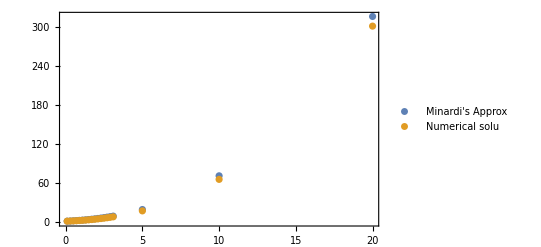

```mathematica
ListPlot[{clist,fList},PlotLegends->{"Minardi's Approx","Numerical solu"},Frame->True,PlotRange->All]
```

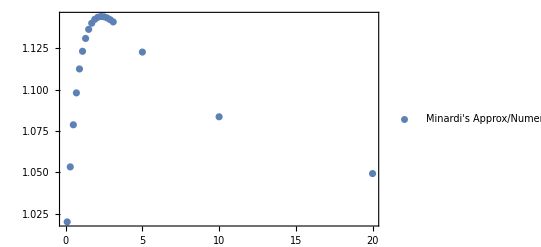

```mathematica
ListPlot[Transpose@{clist[[All,1]],clist[[All,2]]/fList[[All,2]]},PlotLegends->{"Minardi's Approx/Numerical solu"},PlotRange->All,Frame->True]
```

So, we can see that, there are mainly several percentage error by using this formula. And the maximum error is about 15%. So, keep this error in mind about the LHY energy.

## Derivation of GPE and extendedGPE from mean-field energy

### Derivation of GPE

First, we assume the many-body wave function is a product state

Ψ((r⃗)_1,(r⃗)_2,… ,(r⃗)_N)=∑_(i=1)^N ψ((r⃗)_i)

Then, we have

E(ψ,ψ^*)=N∫ⅆr^3(ℏ^2/(2m)(|∇ψ(r)|)^2+V(r)(|ψ(r)|)^2+1/2 N g(|ψ(r)|)^4)

define the Variation

X(ψ,ψ^*)=E(ψ,ψ^*)-μ N∫ⅆ r^3(|ψ(r)|)^2

take the variation of X(ψ,ψ^*), we have

δ X(ψ,ψ^*)=N∫ⅆr^3(ℏ^2/(2m)(∇ψ^*(r)∇δψ(r)+∇ψ(r)∇δψ^*(r))+(V(r)-μ)(ψ^*(r)δ ψ(r)+ψ(r)δ ψ^*(r) )+N g(ψ^2(r)δ ψ^*(r)+(ψ^*)^2(r)δ ψ(r)))
=N∫ⅆr^3(ℏ^2/(2m)(∇ψ(r)∇δψ^*(r))+(V(r)-μ)(ψ(r)δ ψ^*(r) )+N g(ψ^2(r)ψ^*(r)δ ψ^*(r)))+c.c.

for the first part, by using integrating by part method:

∫ⅆr^3(∇ψ(r)∇δψ^*(r))=δψ^*(r)∇ψ(r)|_0^∞-∫ⅆr^3(∇^2 ψ(r)δψ^*(r))=∫ⅆr^3(-∇^2 ψ(r))δψ^*(r)

Them, take the variance to be zero, we have GPE

-ℏ^2/(2m)(∇^2 ψ(r))+(V(r)-μ)ψ(r)+N g(ψ^2(r)ψ^*(r))=0
-ℏ^2/(2m)(∇^2 ψ^*(r))+(V(r)-μ)ψ^*(r)+N g((ψ^*)^2(r)ψ(r))=0

### Derivation of extendedGPE(eGPE)

First, we assume the many-body wave function is a product state

Ψ((r⃗)_1,(r⃗)_2,… ,(r⃗)_N)=∑_(i=1)^N ψ((r⃗)_i)

Then, we have

E(ψ,ψ^*)=N∫ⅆr^3(ℏ^2/(2m)(∇ψ^*(r)∇ψ(r))+V(r)(ψ^*(r)ψ(r))+1/2 N (g(ψ^*(r)ψ(r)))^2+C (ψ^*(r)ψ(r))^(5/2))

define the Variation

X(ψ,ψ^*)=E(ψ,ψ^*)-μ N∫ⅆr^3(ψ^*(r)ψ(r))

take the variation of X(ψ,ψ^*), we have

δ X(ψ,ψ^*)=N∫ⅆr^3(ℏ^2/(2m)(∇^2 ψ(r)δψ^*(r))+(V(r)-μ)(ψ(r)δψ^*(r) )+N g(ψ^2(r)ψ^*(r)δψ^*(r))+(5C)/2(ψ(r))^(5/2)(ψ^*(r))^(3/2)δψ^*(r))+c.c.

where C is constants which already expressed the Last Part.

thus, we have eGPE

-ℏ^2/(2m)(∇^2 ψ(r))+(V(r)-μ)ψ(r)+N g(ψ^*(r)ψ(r))ψ(r)+(5C)/2(ψ(r)ψ^*(r))^(3/2)ψ(r)=0
-ℏ^2/(2m)(∇^2 ψ^*(r))+(V(r)-μ)ψ^*(r)+N g((ψ^*)^2(r)ψ(r))+(5C)/2(ψ^*(r))^(5/2)(ψ(r))^(3/2)=0

### Extended GPE for double species

First, we assume the many-body wave function is a product state

Ψ((r⃗)_1,(r⃗)_2,… ,(r⃗)_N)=∑_(i=1)^N ψ_1((r⃗)_i)∑_(i=1)^N ψ_2((r⃗)_i)

Then, we have

E(ψ_1,ψ_1^*,ψ_2,ψ_2^*)=∫ⅆr^3(ψ_1^* | ψ_2^*).(ℋ_11 | ℋ_12
ℋ_21 | ℋ_22).(ψ_1
ψ_2)+E_LHY

where ℋ_(i,j) represent the Hamiltonian density of fields

ℋ_11=N_1(ℏ^2/(2 m_1)(∇)^2+V_1(r)+1/2 N_1 g_11(ψ_1^*(r)ψ_1(r)))
ℋ_22=N_2(ℏ^2/(2 m_2)(∇)^2+V_2(r)+1/2 N_2(g_22(ψ_2^*(r)ψ_2(r)))^2)
ℋ_12=ℋ_21^†=N_1 N_2 g_12(ψ_1^*(r)ψ_1(r))(ψ_2^*(r)ψ_2(r))

and LHY term has been expressed in the last part.

define the Variation

X(ψ,ψ^*)=E(ψ,ψ^*)-μ_1 N_1∫ⅆr^3(ψ_1^*(r)ψ_1(r))-μ_2 N_2∫ⅆr^3(ψ_2^*(r)ψ_2(r))

Finally, we have eGPE for

ⅈ ℏ(∂ψ_1)/(∂t)=(-(ℏ^2∇^2)/(2 m_1)+V_1+g_11 n_1+g_12 n_2+(δ ℰ_LHY)/(δ n_1))ψ_1
ⅈ ℏ(∂ψ_2)/(∂t)=(-(ℏ^2∇^2)/(2 m_2)+V_2+g_22 n_2+g_12 n_1+(δ ℰ_LHY)/(δ n_2))ψ_2

## eGPE for GPELAB with Minardi approximation

ⅈ ℏ(∂ψ_1)/(∂t)=(-(ℏ^2∇^2)/(2 m_1)+V_1+g_11 n_1+g_12 n_2+(δ ℰ_LHY)/(δ n_1))ψ_1
ⅈ ℏ(∂ψ_2)/(∂t)=(-(ℏ^2∇^2)/(2 m_2)+V_2+g_22 n_2+g_12 n_1+(δ ℰ_LHY)/(δ n_2))ψ_2

where

n_i=N_i ψ_i^*ψ_i=N_i|ψ_i|^2

and

(δ ℰ_LHY)/(δ n_1)=8/(15 π^2)((m_1^(3/2)(g_11))^(5/2)n_1^(1/2))/ℏ^3(5/2 n_1 f(γ,x,y)-(g_22 n_2)/g_11(∂f(γ,x,y))/(∂y))

(δ ℰ_LHY)/(δ n_2)=8/(15 π^2)((m_1^(3/2)(g_11))^(3/2)g_22 n_1^(3/2))/ℏ^3(∂f(γ,x,y))/(∂y)

if we using the approximation formula, we have

ℰ_LHY=8/(15 π^2)((m_1^(3/2)(g_11 n_1))^(5/2))/ℏ^3(1+γ^(3/5)y)^(5/2)

Then,

(δ ℰ_LHY)/(δ n_1)=8/(15 π^2)((m_1^(3/2)(g_11))^(5/2)n_1^(1/2))/ℏ^3(5/2(n_1(1+γ^(3/5)y))^(5/2)-5/2(g_22 n_2)/g_11(1+γ^(3/5)y)^(3/2)γ^(3/5))
=4/(3 π^2)((m_1^(3/2)(g_11))^(5/2)n_1^(3/2))/ℏ^3(1+γ^(3/5)y)^(3/2)

(δ ℰ_LHY)/(δ n_2)=8/(15 π^2)((m_1^(3/2)(g_11))^(3/2)g_22 n_1^(3/2))/ℏ^3 5/2(1+γ^(3/5)y)^(3/2)γ^(3/5)
=4/(3 π^2)(γ^(3/5)(m_1^(3/2)(g_11))^(3/2)g_22 n_1^(3/2))/ℏ^3(1+γ^(3/5)y)^(3/2)

Finally, we have extended GPE as

ⅈ ℏ(∂ψ_1)/(∂t)=(-(ℏ^2∇^2)/(2 m_1)+V_1+g_11 n_1+g_12 n_2+4/(3 π^2)(g_11 m_1^(3/5))/ℏ^3(g_11 n_1 m_1^(3/5)+g_22 n_2 m_2^(3/5))^(3/2))ψ_1
ⅈ ℏ(∂ψ_2)/(∂t)=(-(ℏ^2∇^2)/(2 m_2)+V_2+g_22 n_2+g_12 n_1+4/(3 π^2)(g_22 m_2^(3/5))/ℏ^3(g_11 n_1 m_1^(3/5)+g_22 n_2 m_2^(3/5))^(3/2))ψ_2

Now, we need do DimensionReduction,

ⅈ (∂Ψ_1)/(∂T)=(-(m∇^2)/(2 m_1)+V_1/(ℏ ω)+4π m/m_1(N_1 a_11)/a Ψ_1^*Ψ_1+2π m/m_12(N_2 a_12)/a Ψ_2^*Ψ_2+(128 π^(1/2))/3 a_11/a(m/m_1)^(2/5)( (N_1 a_11)/a(m/m_1)^(2/5)Ψ_1^*Ψ_1+ (N_2 a_22)/a(m/m_2)^(2/5)Ψ_2^*Ψ_2)^(3/2))Ψ_1
ⅈ (∂Ψ_2)/(∂T)=(-(m∇^2)/(2 m_2)+V_2/(ℏ ω)+4π m/m_2(N_2 a_22)/a Ψ_2^*Ψ_2+2π m/m_12(N_1 a_12)/a Ψ_1^*Ψ_1+(128 π^(1/2))/3 a_22/a(m/m_2)^(2/5)( (N_1 a_11)/a(m/m_1)^(2/5)Ψ_1^*Ψ_1+ (N_2 a_22)/a(m/m_2)^(2/5)Ψ_2^*Ψ_2)^(3/2))Ψ_2

where we set V_1 and V_2 as harmonic trap, and it gives the characteristic length and time. Actually, this characteristic length and time can be arbitrary.

g_11=(4π ℏ^2 a_11)/m_1, g_22=(4π ℏ^2 a_22)/m_2, g_12=(2π ℏ^2 a_12)/m_12, m=m_12=(m_1 m_2)/(m_1+m_2)
T=ω t, R⃗=r⃗/a, Ψ=ψ a^(3/2), a=√(ℏ/(m ω))

By the way, we can calculate the Nonlinear-Energy function. (Just for fun, not for GPELAB)

Recall LHY energy term

ℰ_LHY=8/(15 π^2)((m_1^(3/2)(g_11 n_1))^(5/2))/ℏ^3(1+(m_2/m_1)^(3/5)(g_22 n_2)/(g_11 n_1))^(5/2)
=(256 √π ℏ^2)/15(m_1^(-2/5)a_11 n_1+m_2^(-2/5)a_22 n_2)^(5/2)

Do DimensionReduction, we have

ℰ_LHY/(ℏ ω/a^3)=(256 π^(1/2))/15((N_1 a_11)/a(m/m_1)^(2/5)Ψ_1^*Ψ_1+ (N_2 a_22)/a(m/m_2)^(2/5)Ψ_2^*Ψ_2)^(5/2)